```mathematica
Λ = 75 10^-9; (*Unit: meter*)
ωp = 6.18;      (* unit: eV *)
γ = 20 10^-3; (* unit: eV *)
ϵ[ω_] := 1 - ωp^2/(ω (ω + I γ));
α[ω_] := (ϵ[ω]-1)/(ϵ[ω]+2)  ; (* unit: 4 Subscript[πϵ, 0] a^3 *)
a = 25 10^-9; (*Unit: meter*)
ω0 = (3 10^8 6.62 10^-34)/(Λ 1.6 10^-19) ;  (* c/Λ, unit: eV*)
```

```mathematica
ω0
```

16.55

```mathematica
ωxy[k_] := ωp N[√(1/3(1 + (a/Λ)^3 (PolyLog[3, ⅇ^(ⅈ π k)] + PolyLog[3, ⅇ^(-ⅈ π k)])))]; (*unit of k: π / Λ, output unit: eV*)
```

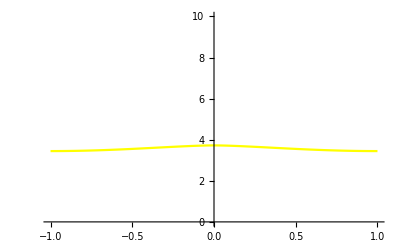

```mathematica
Plot[ωxy[k], {k, -1, 1}, PlotRange->{0, 10},PlotStyle->Yellow]
```

```mathematica
ωz[k_] := ωp N[√(1/3(1 -2 (a/Λ)^3(PolyLog[3, ⅇ^(ⅈ π k)] + PolyLog[3, ⅇ^(-ⅈ π k)])))]; (*unit of k: 1 / Λ, output unit: eV*)
```

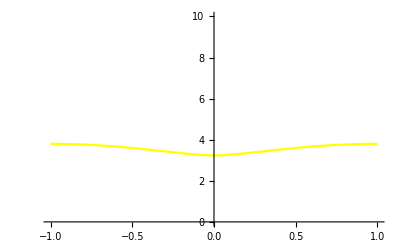

```mathematica
Plot[ωz[k], {k, -1, 1}, PlotRange->{0, 10},PlotStyle->Yellow]
```

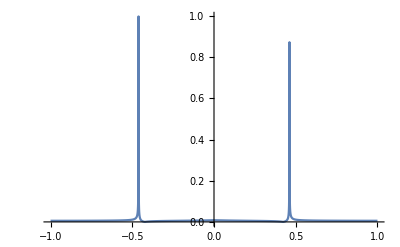

```mathematica
Plot[Abs[((ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]))/(PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))])] /. {ω -> 0.1}, {k, -1, 1}, PlotRange->All]
```

```mathematica
αxy[ω_, k_] := N[α[ω]/(1- α[ω](a/Λ)^3((ω/ω0)^2 (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) ))];
 (*unit: ω eV, k  π/Λ*)
```

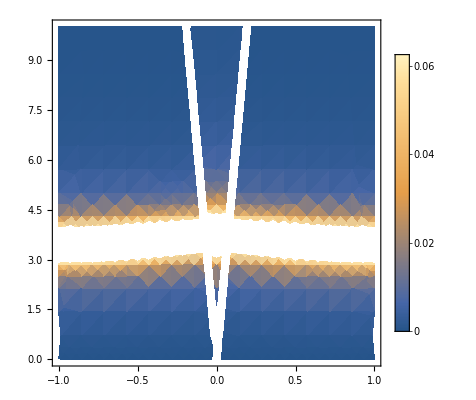

```mathematica
DensityPlot[Im[αxy[ω,k]], {k, -1, 1}, {ω, 0, 10}, PlotLegends->Automatic]
```

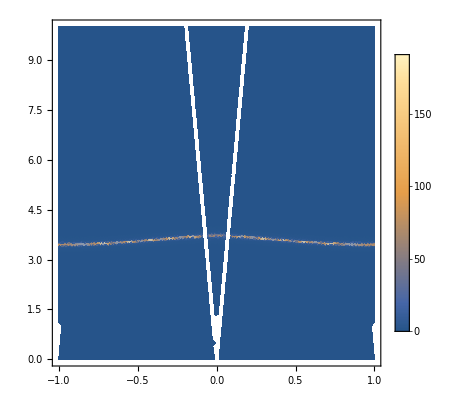

```mathematica
DensityPlot[Im[αxy[ω,k]], {k, -1, 1}, {ω, 0, 10}, PlotPoints->100,PlotLegends->Automatic,PlotRange->All]
```

```mathematica
DensityPlot[N[α[ω]/(1- α[ω](ω/ω0)^3 (a/Λ)^3((ω0/ω) (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω0/ω)^2 (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (ω0/ω)^3(PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) ))],{k, -1, 1}, {ω, 2, 10}, PlotLegends->Automatic]
```

-Graphics-

```mathematica
αz[ω_, k_] := N[α[ω]/(1- α[ω](a/Λ)^3(-2ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) +2(PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) ))];
 (*unit: ω eV, k  π/Λ*)
```

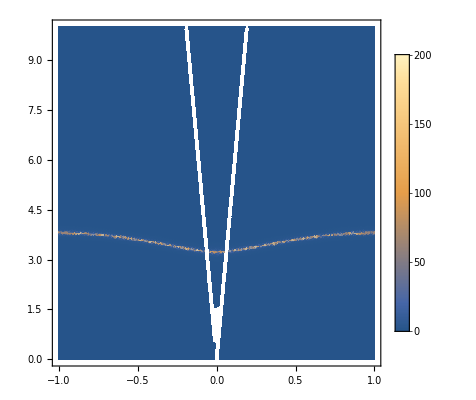

```mathematica
DensityPlot[Im[αz[ω,k]], {k, -1, 1}, {ω, 0, 10}, PlotPoints->100,PlotLegends->Automatic,PlotRange->All]
```

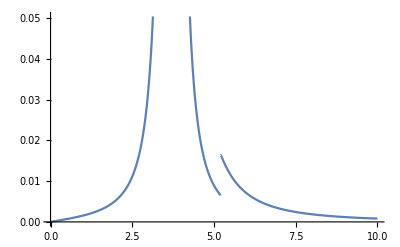

```mathematica
Plot[Im[αxy[ω, 0.1]], {ω, 0,10}]
```

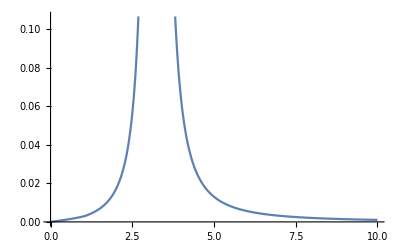

```mathematica
Plot[Im[αz[ω, 0.02]], {ω, 0,10}]
```

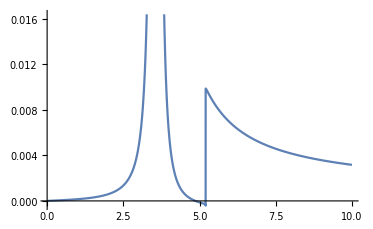

```mathematica
Plot[Im[(1- α[ω](a/Λ)^3((ω/ω0)^2 (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) )) /. k -> 0.1], {ω, 0, 10},PlotPoints->200]
```

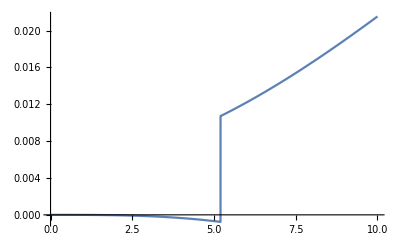

```mathematica
Plot[Im[((a/Λ)^3((ω/ω0)^2 (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) )) /. k -> 0.1], {ω, 0, 10},PlotPoints->200]
```

```mathematica
ω0 π 0.1
```

5.19934

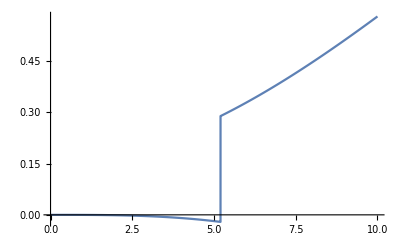

```mathematica
Plot[Im[(((ω/ω0)^2 (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) + ⅈ(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) - (PolyLog[3, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[3, ⅇ^(ⅈ (ω/ω0+ π k))]) )) /. k -> 0.1], {ω, 0, 10},PlotPoints->200]
```

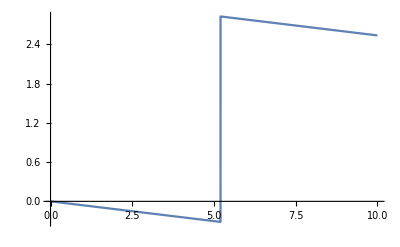

```mathematica
Plot[Im[ (PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[1, ⅇ^(ⅈ (ω/ω0+ π k))]) /. k -> 0.1], {ω, 0, 10},PlotPoints->200]
```

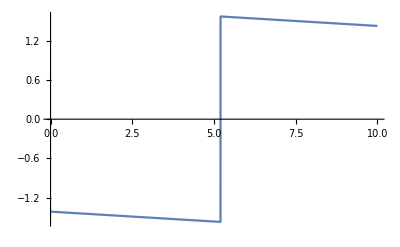

```mathematica
Plot[ Im[PolyLog[1, ⅇ^(ⅈ (ω/ω0- π k))]] /. k -> 0.1, {ω, 0, 10},PlotPoints->200]
```

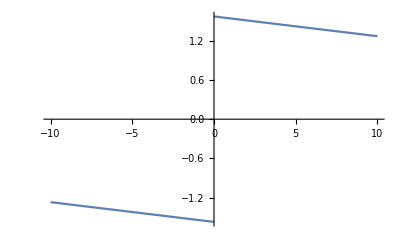

```mathematica
Plot[ Im[PolyLog[1, ⅇ^(ⅈ ω/ω0)]] , {ω, -10, 10},PlotPoints->200]
```

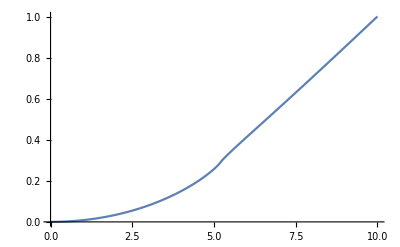

```mathematica
Plot[Im[(ω/ω0) (PolyLog[2, ⅇ^(ⅈ (ω/ω0- π k))]+PolyLog[2, ⅇ^(ⅈ (ω/ω0+ π k))]) /. k -> 0.1], {ω, 0, 10},PlotPoints->200]
```

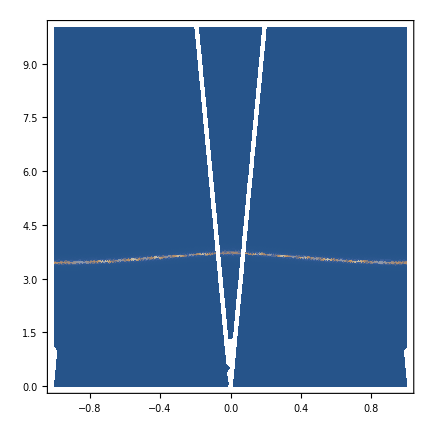
```mathematica
Show[-Graphics-,-Graphics-]
```

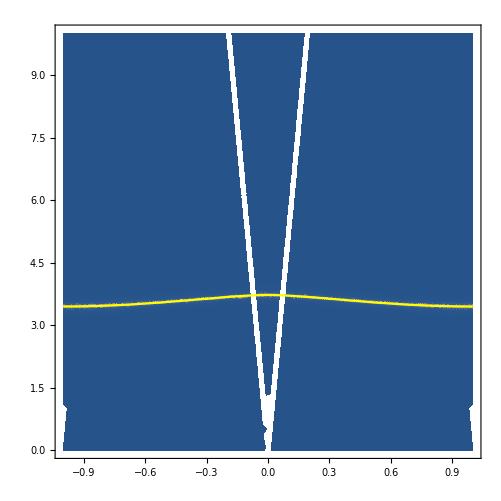

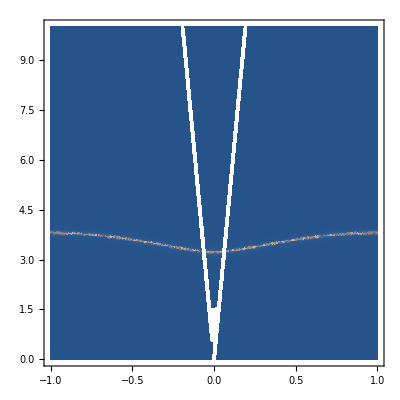
```mathematica
Show[-Graphics-,-Graphics-]
```

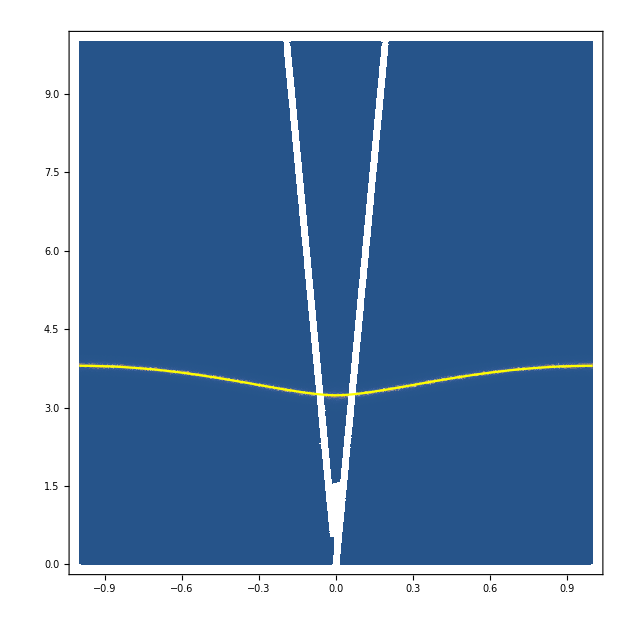

```mathematica
4/ω0
```

0.241692

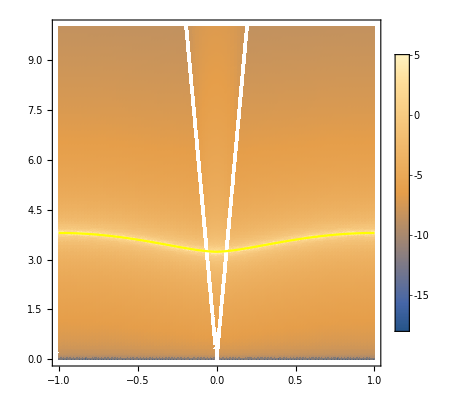

```mathematica
Show[DensityPlot[Log[Im[αz[ω,k]]], {k, -1, 1}, {ω, 0, 10}, PlotPoints->100,PlotLegends->Automatic,PlotRange->All],-Graphics-]
```

```mathematica
N[{Sum[ⅇ^(ⅈ θ n)/n , {n, 1,1000}], PolyLog[1, ⅇ^(ⅈ θ)]}/. θ -> π/10]
```

{1.16246+1.41056 ⅈ,1.16197+1.41372 ⅈ}